```mathematica
coordinatesPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/Helpers/Text files/coordinates.txt";
firstMethodPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/Helpers/Text files/ConvexHullPoints(MethodI).txt";
secondMethodPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/Helpers/Text files/ConvexHullPoints(MethodII).txt";

numberOfPoints = ToExpression[
Import[coordinatesPath, {"Lines", 1} ]
];
```

```mathematica
points = {};
For[i = 2, i < numberOfPoints* 2 + 2, i+= 2, 
AppendTo[points,Point[ToExpression[
Take[
Import[coordinatesPath,"Words"],{i, i+1}]
]
]
]
]
```

```mathematica
numberOfConvexHullPoints = ToExpression[Import[firstMethodPath, {"Lines", 1}]];
convexHullPoints = {};
For[i = 2, i < numberOfConvexHullPoints * 2 + 2, i+= 2, AppendTo[convexHullPoints,ToExpression[Take[Import[firstMethodPath, "Words"],{i, i+1}]]]
]
AppendTo[convexHullPoints, Part[convexHullPoints, 1]]
```

{{1.49489,0.377652},{0.815421,-0.468176},{-0.32008,-0.58109},{-1.63423,-0.617773},{-1.54083,0.946829},{1.28229,0.708425},{1.49489,0.377652}}

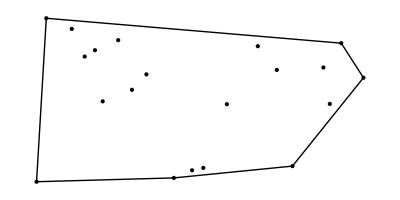

```mathematica
Graphics[{points,Line[convexHullPoints]}]
```